```mathematica
A//MatrixForm
```

(4.33 | -1.12 | -1.08 | 1.14
-1.12 | 4.33 | 0.24 | -1.22
-1.08 | 0.24 | 7.21 | -3.22
1.14 | -1.22 | -3.22 | 5.43)

```mathematica
A={{4.33,-1.12,-1.08,1.14},{-1.12,4.33,0.24,-1.22},{-1.08,0.24,7.21,-3.22},{1.14,-1.22,-3.22,5.43}};
f={0.3,0.5,0.7,0.9};
r={{}};
z={{}};
x={{2,-1,1,1}};
a={{}};
b={{}};
r[[1]]=f-A.x[[1]]
z[[1]]=r[[1]]
```

{-9.54,8.05,-0.89,-4.81}

{-9.54,8.05,-0.89,-4.81}

```mathematica
For[k=2,k<6,k++,
a=Append[a,{}];
a[[k]]=(r[[k-1]].r[[k-1]])/(A.z[[k-1]].z[[k-1]]);
x=Append[x,{}];
x[[k]]=x[[k-1]]+a[[k]]*z[[k-1]];
r=Append[r,{}];
r[[k]]=r[[k-1]]-a[[k]]*A.z[[k-1]];
b=Append[b,{}];
b[[k]]=(r[[k]].r[[k]])/(r[[k-1]].r[[k-1]]);

z=Append[z,{}];
z[[k]]=r[[k]]+b[[k]]*z[[k-1]];
]
```

```mathematica
Table[Map[N,x[[i]]],{i,1,5}]
```

{{2.,-1.,1.,1.},{0.479561,0.28297,0.858156,0.233406},{0.222514,0.402293,0.30967,0.427282},{0.0894099,0.229494,0.277127,0.376321},{0.100579,0.225667,0.260999,0.350105}}

```mathematica
ClearAll[a,b,c,d]
```

```mathematica
A[[4]]
```

{0.55,0.43,0.35,1}

```mathematica
NSolve[{4.33*a-1.12*b-1.08*c+1.14*d==0.3,-1.12*a+4.33*b+0.24*c-1.22*d==0.5,-1.08*a+0.24*b+7.21*c-3.22*d==0.7,1.14*a-1.22*b-3.22*c+5.43*d==0.9},{a,b,c,d}]
```

{{a→0.100579,b→0.225667,c→0.260999,d→0.350105}}

```mathematica
f
```

{0.3,0.5,0.7,0.9}

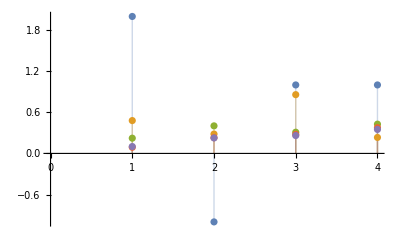

```mathematica
ListPlot[Table[Map[N,x[[i]]],{i,1,5}],Filling->Axis]
```

```mathematica
Show[ListPlot[Table[N/@x⟦i⟧,{i,1,5}],PlotTheme->"Marketing",Filling->Axis],ImageSize->Large]
```

-Graphics-

```mathematica
A={{2x1,-5x2,4x3},{1x1,0,5x3},{3x1,1x2,-2x3}}
```

```mathematica
A={{4.33,-1.12,-1.08,1.14},{-1.12,4.33,0.24,-1.22},{-1.08,0.24,7.21,-3.22},{1.14,-1.22,-3.22,5.43}}
```

{{4.33,-1.12,-1.08,1.14},{-1.12,4.33,0.24,-1.22},{-1.08,0.24,7.21,-3.22},{1.14,-1.22,-3.22,5.43}}

```mathematica
%//MatrixForm
```

(4.33 | -1.12 | -1.08 | 1.14
-1.12 | 4.33 | 0.24 | -1.22
-1.08 | 0.24 | 7.21 | -3.22
1.14 | -1.22 | -3.22 | 5.43)

```mathematica
f={0.3,0.5,0.7,0.9}
```

{0.3,0.5,0.7,0.9}

```mathematica
Show[ListPlot[Table[N/@x⟦i⟧,{i,1,7}],PlotTheme->"Marketing",Filling->Axis],ImageSize->Large]
```

-Graphics-

```mathematica
NSolve[{a+0.17*b-0.25*c+0.54*d==0.3,0.47*a+b+0.67*c-0.32*d==0.5,-0.11*a+0.35*b+c-0.74*d==0.7,0.55*a+0.43*b+0.35*c+d==0.9},{a,b,c,d}]
```

```mathematica
scalar[x_,y_]:=Sum[x[[n]]*y[[n]],{n,1,Length[x]}];
```